Barometric relation

```mathematica
eqn 1 = Dt[2 NN k T,r]+(G Msun M NN)/r^2==0;
```

Thermal conductivity

```mathematica
eqn 2=κ==κ0 T^n;
```

Solving for the temperature

```mathematica
1/r^2 Dt[r^2 κ Dt[T,r],r];
% /. Solve[eqn 2,κ][[1]];
% /. T-> A r^α;
% /. {Dt[κ0,_]:>0,Dt[n,_]:>0,Dt[A,_]:>0,Dt[α,_]:>0};
PowerExpand[%];
Simplify[%];
Solve[%==0,α][[2]];
eqn 3=Simplify[T==T0*(a/r)^-α/.%]
```

T==(a/r)^(1/(1+n)) T0

Solution for the density

```mathematica
eqn 1;
% /. Solve[eqn 3,T][[1]];
% /. {Dt[k,_]:>0,Dt[T0,_]:>0,Dt[a,_]:>0,Dt[n,_]:>0};
%/.NN-> NN[r];
NN[r]/.DSolve[{%,NN[a]==N0},NN[r],r][[1]];
eqn 4=NN==Simplify[%];
```

When n == 0

```mathematica
eqn 4[[2]];
Log[%];
PowerExpand[%];
Limit[%,n->0];
Exp[%];
PowerExpand[%];
Simplify[%];
eqn 6=NN==%;
```

Pressure for n≠0

```mathematica
2NN k T;
% /. Solve[eqn 3,T][[1]];
% /. Solve[eqn 4,NN][[1]];
% /. Solve[p0==2 N0 k T0,T0][[1]];
PowerExpand[%];
Simplify[%];
eqn 7=p==%;
```

Pressure for n == 0

```mathematica
2NN k T;
% /. Solve[eqn 3,T][[1]];
% /. Solve[eqn 6,NN][[1]];
% /. Solve[p0==2 N0 k T0,T0][[1]];
Simplify[%];
eqn 8=p==%;
```

Pressure at infinity

```mathematica
eqn 7[[2]];
Limit[%,r->∞,Assumptions->{n>0}];
p==%;
eqn 9=%;
```

Conservation of momentum

```mathematica
eqn 10= NN M v Dt[v,r]==-Dt[2 NN k T,r]-G NN M Msun/r^2;
```

Continuity equation

```mathematica
eqn 11=Dt[r^2 NN v,r]==0;
```

Solution of the continuity equation

```mathematica
eqn 12=NN v r^2==N0 v0 a^2;
```

Dimensionless reduction to the conservation of momentum

```mathematica
eqn 10;
% /. Solve[eqn 12,NN][[1]];
% /. T-> T0 τ;
% /. v-> √(2 ψ k T0/M);
% /. HoldPattern[Dt[z_,r]]:> Dt[z,ξ]/Dt[r,ξ];
% /. r-> ξ a;
% /. {Dt[k,_]:>0,Dt[a,_]:>0,Dt[N0,_]:>0,Dt[v0,_]:>0,Dt[T0,_]:>0,
Dt[M,_]:>0};
Simplify[%];
% /. Msun-> λ *(2 a k T0)/(G M);
Simplify[%,{M>0,T0>0,N0>0,v0>0,ψ>0,k>0}];
eqn 13=%;
```

Let us verify that this is equivalent to equation 13 in the paper

```mathematica
eqn 13 orig = Dt[ψ,ξ](1-τ/ψ)==-2 ξ^2 Dt[τ/ξ^2,ξ]-(2λ)/ξ^2;
```

```mathematica
eqn 13 orig;
%/. Solve[eqn 13,Dt[ψ,ξ]][[1]];
Simplify[%]
```

True

Solving the momentum equation when the temperature is constant

```mathematica
eqn 13;
% /. τ->1;
% /. ψ->ψ[ξ];
D[(ψ[ξ]-Log[ψ[ξ]]), ξ]/.Solve[%,ψ'[ξ]][[1]];
Simplify[%];
Integrate[%,ξ];
%-(%/.ξ->1);
Simplify[%];
ψ-Log[ψ]-(ψ0-Log[ψ0])==%;
eqn 14=%;
```

Let us verify that this result is equivalent to equation 14 in the paper

```mathematica
eqn 14 orig=ψ-Log[ψ]==ψ0-Log[ψ0]+4 Log[ξ]-2λ(1-1/ξ);
```

```mathematica
eqn 14 orig;
%/.Solve[eqn 14,λ][[1]];
Simplify[%]
```

True

Solution when τ == 0

```mathematica
eqn 13;
% /. τ->0;
% /. ψ->ψ[ξ];
Simplify[%];
ψ[ξ]/.DSolve[%,ψ[ξ],ξ][[2]];
%-(%/.ξ->b/a)+ψ[b/a];
ψ[ξ]==Simplify[%];
eqn 15=%;
```

Definition of Y

```mathematica
Y def=Y==4 Log[ξ]-2λ(1-1/ξ);
```

Definition of Z

```mathematica
Z def=Z==ψ-Log[ψ];
```

From the conditions that the minima of Y and Z must coincide

```mathematica
eqn 14;
%/.Solve[D[Y def[[2]], ξ]==0,ξ][[1]];
%/.Solve[D[Z def[[2]], ψ]==0,ψ][[1]];
1-%[[1]]==Simplify[1-%[[2]]];
eqn 16=%;
```

```mathematica
eqn 14;
Simplify[%[[1]]+eqn 16[[1]]]==Simplify[%[[2]]+eqn 16[[2]]];
eqn 17=%;
```

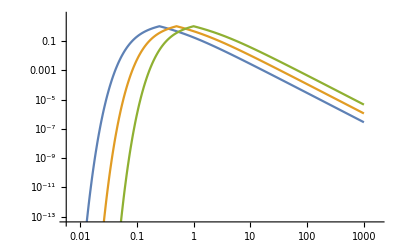

```mathematica
eqn 17;
ψ/.Solve[%,ψ][[1]];
√%;
Table[%/.λ->λval,{λval,{0.5,1,2}}];
LogLogPlot[%,{ξ,10^-2,10^3}]
```

Continuity in n dimensions (not to be confused with the n used for the temperature power law)

```mathematica
n dimension continuity=NN v==N0 v0(a/r)^(n-1);
```

Re - deriving the dimensionless momentum equation

```mathematica
eqn 10;
% /. Solve[n dimension continuity,NN][[1]];
% /. T-> T0 τ;
% /. v-> √(2 ψ k T0/M);
% /. HoldPattern[Dt[z_,r]]:> Dt[z,ξ]/Dt[r,ξ];
% /. r-> ξ a;
% /. {Dt[k,_]:>0,Dt[a,_]:>0,Dt[N0,_]:>0,Dt[v0,_]:>0,Dt[T0,_]:>0,
Dt[M,_]:>0,Dt[n,_]:>0};
Simplify[%];
% /. Msun-> λ *(2 a k T0)/(G M);
Simplify[%,{M>0,T0>0,N0>0,v0>0,ψ>0,k>0}];
%/.ψ->ψ[ξ];
% /. τ->1;
D[(ψ[ξ]-Log[ψ[ξ]]), ξ]/.Solve[%,ψ'[ξ]][[1]];
Simplify[%];
Integrate[%,ξ];
%-(%/.ξ->1);
ψ-Log[ψ]==ψ0-Log[ψ0]+%;
eqn 18=%;
```

Continuity equation for an offset cone

```mathematica
eqn 19=NN v==N0 v0((a-s)/(r-s))^2;
```

Corresponding dimensionless momentum equation

```mathematica
eqn 10;
% /. Solve[eqn 19,NN][[1]];
% /. T-> T0 τ;
% /. v-> √(2 ψ k T0/M);
% /. HoldPattern[Dt[z_,r]]:> Dt[z,ξ]/Dt[r,ξ];
% /. r-> ξ a;
% /. {Dt[k,_]:>0,Dt[a,_]:>0,Dt[N0,_]:>0,Dt[v0,_]:>0,Dt[T0,_]:>0,
Dt[M,_]:>0,Dt[n,_]:>0,Dt[s,_]:>0};
Simplify[%];
% /. Msun-> λ *(2 a k T0)/(G M);
Simplify[%,{M>0,T0>0,N0>0,v0>0,ψ>0,k>0}];
%/.ψ->ψ[ξ];
% /. τ->1;
D[(ψ[ξ]-Log[ψ[ξ]]), ξ]/.Solve[%,ψ'[ξ]][[1]];
Simplify[%];
Integrate[%,ξ];
%-(%/.ξ->1);
ψ-Log[ψ]==ψ0-Log[ψ0]+%;
eqn 20=%;
```

```mathematica
eqn 20;
ξ/.Simplify[Solve[∂_ξ %[[2]]==0,ξ]][[2]];
Simplify[%,a>0&&λ>0];
eqn 21=ξ==%;
```

Coronal heating

```mathematica
coronal heating mk1=1/2 M(Nm vm^3 b^2/r^2-NN v^3);
```

```mathematica
coronal heating mk1;
%/.Solve[eqn 12,NN][[1]];
%/.((Solve[eqn 12,NN][[1]])/.{r->rm,NN->Nm,v->vm});
% /. v-> √(2 ψ k T0/M);
% /. vm-> √(2ψm k T0/M);
% /. rm-> b;
Simplify[%];
coronal heating mk2=%;
```

Definition of w

```mathematica
coronal heating mk2-2 v NN k T0;
%/(2k NN T0);
% /. Solve[eqn 12,NN][[1]];
Simplify[%];
w def=%;
```

Ratio between thermal and transport velocity

```mathematica
(w def)/(√(3 k T0/M));
% /. v-> √(2ψ k T0/M);
Simplify[%,{k>0,T0>0,ψ>0,M>0}];
eqn 22=w/u==%;
```

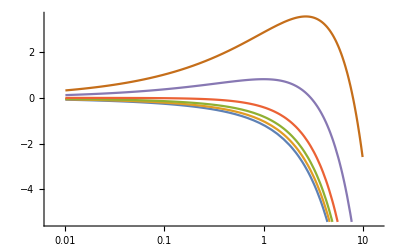

```mathematica
eqn 22[[2]];
Table[%/.ψm->ψmval,{ψmval,{0.1,0.5,1,2,5,10}}];
LogLinearPlot[%,{ψ,0.01,10}]
```

solar mass loss

```mathematica
eqn 23=Dt[Msun,t]==4π a^2 N0 M v0;
```

Components of the velocity

```mathematica
eqn 24={vr==vm,vθ==0,vφ==ω(r-b)Sin[θ]};
```

Streamline

```mathematica
vr/(vφ/r/Sin[θ]);
% /.Solve[eqn 24,{vr,vθ,vφ}][[1]];
r'[φ]==(%/.r->r[φ]);
D[(r[φ]/b-1-Log[r[φ]/b]), φ]/.Solve[%,r'[φ]][[1]];
Simplify[%];
eqn 25=r[φ]/b-1-Log[r[φ]/b]==%*(φ-φ0);
```

The magnetic field is parallel to the velocity

```mathematica
1/r^2 Dt[r^2 Br,r]+1/(r Sin[θ])Dt[Bθ Sin[θ],θ]+1/(r Sin[θ])Dt[Bφ,φ];
%/. {Br-> B0 vr/vm,Bθ-> B0 vθ/vm,Bφ-> B0 vφ/vm};
% /.Solve[eqn 24,{vr,vθ,vφ}][[1]];
% /. {Dt[b,_]:>0,Dt[vm,_]:>0,Dt[ω,_]:>0,Dt[θ,_]:>0,Dt[r,_]:>0};
% /. Dt[B0,φ]->0;
Simplify[%];
% /. B0-> B0[r];
B0[r]/.DSolve[{%==0,B0[b]==B[θ]},B0[r],r][[1]];
%/vm{vr,vθ,vφ};
% /.Solve[eqn 24,{vr,vθ,vφ}][[1]];
Simplify[%];
Thread[{Br,Bθ,Bφ}==%];
eqn 26=%;
```

I think that equation 27 is wrong, the locii where the components of the magnetic field are equation is

```mathematica
Br==Bφ/.Solve[eqn 26,{Br,Bθ,Bφ}][[1]];
r/.Solve[%,r][[1]]
```

(Csc[θ] (vm+b ω Sin[θ]))/ω

Calculation of torque

```mathematica
(Br Bφ)/(4π)r Sin[θ];
%*r^2;
%/.Solve[eqn 26,{Br,Bθ,Bφ}][[1]];
Integrate[%,{φ,0,2π}];
Integrate[%*Sin[θ],{θ,0,π}];
torque mk 1=%
```

∫_0^π -(b^4 (b-r) ω B[θ]^2 Sin[θ]^3)/(2 r vm)ⅆθ

```mathematica
torque mk 1;
% /. B[θ]-> B0 Cos[θ]
```

-(2 b^4 B0^2 (b-r) ω)/(15 r vm)